## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
```

## Equation and and Eigenvalue function

```mathematica
<<"Definitions/Teukolsky.wl"
<<"Definitions/Eigenvalues.wl"
```

```mathematica
Eq=EqRadial/.RuleKRadial;
```

```mathematica
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real?Negative]:=ℰ[𝓈,ℓ,-𝓂,-𝒸];
ℰ[𝓈_Integer?Negative,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]:=ℰ[-𝓈,ℓ,𝓂,𝒸];
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]:=ℰ[𝓈,ℓ,𝓂][𝒸];
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer]/;(ℓ≥Max[Abs[𝓈],Abs[𝓂]]):=ℰ[𝓈,ℓ,𝓂]=Interpolation[Import@GetSWSHEigenFile[𝓈,ℓ,𝓂]]
```

## Parameter rules and equation simplification

```mathematica
RuleR={R->Function[x,(x/τ)^(-s-ⅈ χ/τ)f[x]]};
nCoef=8;
RuleF={f->Function[x,∑_(n=0)^nCoef 𝒶[n] x^n]};
RuleBoundaryBHole[1]={𝒶[0]->1};
RuleBoundaryBHole[-1]={𝒶[0]->(-ℬ τ^4)/(4 (ⅈ τ/2+χ) χ)};
EquationF=PowerExpand@Simplify[(x/τ)^(s+ⅈ χ/τ)x (x+τ) (Eq/.RuleR)];
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),ℬ->Sqrt[(λ+s(s+1))^2-4((𝒥 ω̄)/rp)^2+4m (𝒥 ω̄)/rp],  
λ->((𝒥 ω̄)/rp)^2-2m((𝒥 ω̄)/rp)+𝔈-s(s+1)};
RuleEigenParamCoef={𝔈->(EigenCoef/.Ruleκpm).Table[((𝒥 ω̄)/rp)^(n-1),{n,Length@EigenCoef}]+s(s+1)};
RuleEigenParamLeaver={𝔈->EigenLeaver[s,l,m,(𝒥 ω̄)/rp]};
RuleEigenParam={𝔈->ℰ[s,l,m,(𝒥 ω̄)/rp]};
RuleAllParams=RuleParams~Join~RuleEigenParam;
```

```mathematica
ReplaceParams[𝓈_,ℓ_,𝓂_,𝒿_]:=PowerExpand[(#1/.RuleBoundaryBHole[𝓈])//.RuleAllParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}]&;
ReplaceParams[𝓈_,ℓ_,𝓂_,𝒿_,𝓌_]:=PowerExpand[(#1/.RuleBoundaryBHole[𝓈])//.RuleAllParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿,ω̄->𝓌}]&;
```

```mathematica
FSeriesCoef=Chop@First@Solve[CoefficientList[EquationF/.RuleF,x][[;;nCoef+1]]==0,Table[𝒶[n],{n,1,nCoef}]//Evaluate];
```

## Equation solver definition

```mathematica
x0=10^-14.;
xM:=4000/ω̄;
```

```mathematica
ClearAll@SolveωF;
SolveωF[𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝒿:{__?NumberQ}|𝒿_?NumberQ]:=SolveωF[𝓈,ℓ,𝓂,𝒿,Range[0.0001,0.65,0.004]]
SolveωF[𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝒿:{__?NumberQ}|𝒿_?NumberQ,{omega__?NumberQ}]/;And@@Thread[0<𝒿<1]&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Block[{SolFInf,eqF,ωlist,delω,ics},
Print["𝓈 = ",𝓈,"; 𝒥 = ",#1];
{eqF,delω,ics}=ReplaceParams[𝓈,𝓂,ℓ,#1][{EquationF,m Ω̄,({f[x0],f'[x0]}/.RuleF/.FSeriesCoef)}];
ωlist=DeleteCases[{omega},delω];ParallelTable[{#1,ω̄,f[xM]}/.First@NDSolve[{eqF==0,{f[x0],f'[x0]}==ics},f,{x,x0,xM}],{ω̄,ωlist}]
]&/@Flatten[{𝒿}]//Flatten[#,1]&;
```

𝓈 = 1; 𝒥 = 0.9

𝓈 = -1; 𝒥 = 0.9

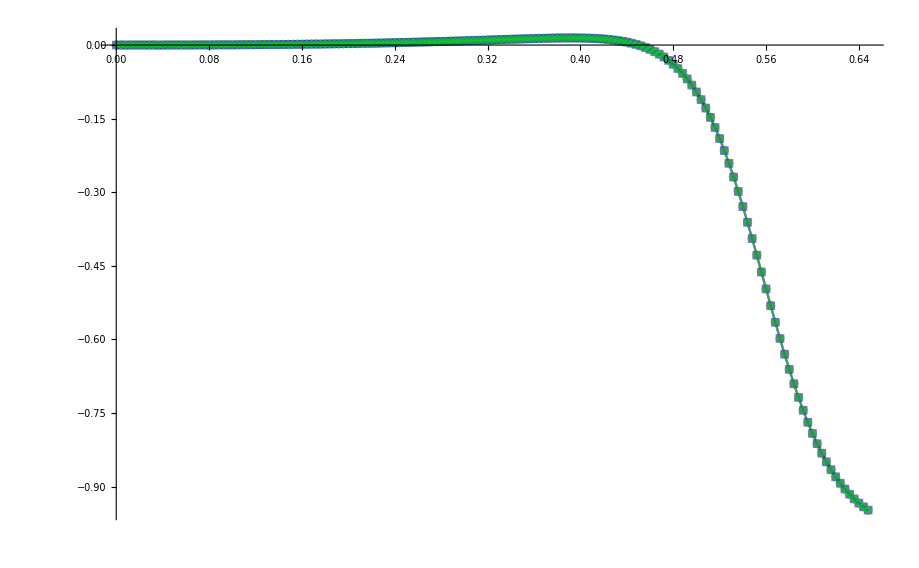

```mathematica
testP=SolveωF[1,1,1,0.9];
testM=SolveωF[-1,1,1,0.9];
pltb=({#1,1/τ^4 Abs[#2/#3]^2-1}//ReplaceParams[1,1,1,0.9,#1])&@@@({testM[[All,2]],testM[[All,3]],testP[[All,3]]}ᵀ);
plt0=(Formatϕ0@@@testP)[[All,{2,3}]];
plt2=(Formatϕ2@@@testM)[[All,{2,3}]];
ListPlot[{pltb,plt0,plt2},PlotMarkers->Automatic,Joined->True,PlotStyle->Thread[{{Red,Blue,Green},Opacity[0.5]}]]
```

## Start calculation and export data

```mathematica
Formatϕ0=({#1,#2,-(ω̄ τ^2/χ Abs[𝒶[0]]^2)/Abs[#3]^2,Abs@#3}//ReplaceParams[1,1,1,#1,#2])&;
Formatϕ2=({#1,#2,-1/(1+(ℬ^2 τ^2 Abs[#3]^2)/(16 ω̄ χ(τ^2/4+χ^2)Abs[𝒶[0]]^2)),Abs@#3}//ReplaceParams[-1,1,1,#1,#2])&;
FormatϕBoth=({#1,#2,-1/(1+(ℬ^2 τ^2 Abs[#3]^2)/(16 ω̄ χ(τ^2/4+χ^2)Abs[𝒶[0]]^2)),Abs@#3}//ReplaceParams[-1,1,1,#1,#2])&;
```

```mathematica
Omega={0,Round[(1+√(1-#^2)) 0.6,0.05],Round[1/450 Round[(1+√(1-#^2)) 0.6,0.05],0.0005]}&;
OmegaDetailed={0,First@TakeSmallest[{#,Round[(1+√(1-#^2)) 0.6,0.05]},1],First@TakeSmallest[{Ceiling[0.01#,0.0001],Round[1/450 Round[(1+√(1-#^2)) 0.6,0.05],0.0005]},1]}&;
```

```mathematica
PutAppendCSV[file_,data_?ArrayQ]:=WriteString[file,ExportString[data,"CSV"],"\n"];
```

```mathematica
Spin=Range[0.01,0.99,0.01]∪{0.995,0.999,0.9995,0.9999};
```

```mathematica
Quiet@DeleteFile[GetZFile[1,1,1,"detailed"]];
PutAppendCSV[GetZFile[1,1,1,"detailed"],Formatϕ0@@@SolveωF[1,1,1,#,0.0001+Range@@OmegaDetailed[#]]]&/@Spin;
Close[GetZFile[1,1,1,"detailed"]];
```

𝓈 = 1; 𝒥 = 0.01

𝓈 = 1; 𝒥 = 0.02

𝓈 = 1; 𝒥 = 0.03

𝓈 = 1; 𝒥 = 0.04

𝓈 = 1; 𝒥 = 0.05

𝓈 = 1; 𝒥 = 0.06

𝓈 = 1; 𝒥 = 0.07

𝓈 = 1; 𝒥 = 0.08

𝓈 = 1; 𝒥 = 0.09

𝓈 = 1; 𝒥 = 0.1

𝓈 = 1; 𝒥 = 0.11

𝓈 = 1; 𝒥 = 0.12

𝓈 = 1; 𝒥 = 0.13

𝓈 = 1; 𝒥 = 0.14

𝓈 = 1; 𝒥 = 0.15

𝓈 = 1; 𝒥 = 0.16

𝓈 = 1; 𝒥 = 0.17

𝓈 = 1; 𝒥 = 0.18

𝓈 = 1; 𝒥 = 0.19

𝓈 = 1; 𝒥 = 0.2

𝓈 = 1; 𝒥 = 0.21

𝓈 = 1; 𝒥 = 0.22

𝓈 = 1; 𝒥 = 0.23

𝓈 = 1; 𝒥 = 0.24

𝓈 = 1; 𝒥 = 0.25

𝓈 = 1; 𝒥 = 0.26

𝓈 = 1; 𝒥 = 0.27

𝓈 = 1; 𝒥 = 0.28

𝓈 = 1; 𝒥 = 0.29

𝓈 = 1; 𝒥 = 0.3

𝓈 = 1; 𝒥 = 0.31

𝓈 = 1; 𝒥 = 0.32

𝓈 = 1; 𝒥 = 0.33

𝓈 = 1; 𝒥 = 0.34

𝓈 = 1; 𝒥 = 0.35

𝓈 = 1; 𝒥 = 0.36

𝓈 = 1; 𝒥 = 0.37

𝓈 = 1; 𝒥 = 0.38

𝓈 = 1; 𝒥 = 0.39

𝓈 = 1; 𝒥 = 0.4

𝓈 = 1; 𝒥 = 0.41

𝓈 = 1; 𝒥 = 0.42

𝓈 = 1; 𝒥 = 0.43

𝓈 = 1; 𝒥 = 0.44

𝓈 = 1; 𝒥 = 0.45

𝓈 = 1; 𝒥 = 0.46

𝓈 = 1; 𝒥 = 0.47

𝓈 = 1; 𝒥 = 0.48

𝓈 = 1; 𝒥 = 0.49

𝓈 = 1; 𝒥 = 0.5

𝓈 = 1; 𝒥 = 0.51

𝓈 = 1; 𝒥 = 0.52

𝓈 = 1; 𝒥 = 0.53

𝓈 = 1; 𝒥 = 0.54

𝓈 = 1; 𝒥 = 0.55

𝓈 = 1; 𝒥 = 0.56

𝓈 = 1; 𝒥 = 0.57

𝓈 = 1; 𝒥 = 0.58

𝓈 = 1; 𝒥 = 0.59

𝓈 = 1; 𝒥 = 0.6

𝓈 = 1; 𝒥 = 0.61

𝓈 = 1; 𝒥 = 0.62

𝓈 = 1; 𝒥 = 0.63

𝓈 = 1; 𝒥 = 0.64

𝓈 = 1; 𝒥 = 0.65

𝓈 = 1; 𝒥 = 0.66

𝓈 = 1; 𝒥 = 0.67

𝓈 = 1; 𝒥 = 0.68

𝓈 = 1; 𝒥 = 0.69

𝓈 = 1; 𝒥 = 0.7

𝓈 = 1; 𝒥 = 0.71

𝓈 = 1; 𝒥 = 0.72

𝓈 = 1; 𝒥 = 0.73

𝓈 = 1; 𝒥 = 0.74

𝓈 = 1; 𝒥 = 0.75

𝓈 = 1; 𝒥 = 0.76

𝓈 = 1; 𝒥 = 0.77

𝓈 = 1; 𝒥 = 0.78

𝓈 = 1; 𝒥 = 0.79

𝓈 = 1; 𝒥 = 0.8

𝓈 = 1; 𝒥 = 0.81

𝓈 = 1; 𝒥 = 0.82

𝓈 = 1; 𝒥 = 0.83

𝓈 = 1; 𝒥 = 0.84

𝓈 = 1; 𝒥 = 0.85

𝓈 = 1; 𝒥 = 0.86

𝓈 = 1; 𝒥 = 0.87

𝓈 = 1; 𝒥 = 0.88

𝓈 = 1; 𝒥 = 0.89

𝓈 = 1; 𝒥 = 0.9

𝓈 = 1; 𝒥 = 0.91

𝓈 = 1; 𝒥 = 0.92

𝓈 = 1; 𝒥 = 0.93

𝓈 = 1; 𝒥 = 0.94

𝓈 = 1; 𝒥 = 0.95

𝓈 = 1; 𝒥 = 0.96

𝓈 = 1; 𝒥 = 0.97

𝓈 = 1; 𝒥 = 0.98

𝓈 = 1; 𝒥 = 0.99

𝓈 = 1; 𝒥 = 0.995

𝓈 = 1; 𝒥 = 0.999

𝓈 = 1; 𝒥 = 0.9995

𝓈 = 1; 𝒥 = 0.9999

```mathematica
Quiet@DeleteFile[GetZFile[-1,1,1,"detailed"]];
PutAppendCSV[GetZFile[-1,1,1,"detailed"],Formatϕ2@@@SolveωF[-1,1,1,#,0.0001+Range@@OmegaDetailed[#]]]&/@Spin;
Close[GetZFile[-1,1,1,"detailed"]];
```

𝓈 = -1; 𝒥 = 0.01

𝓈 = -1; 𝒥 = 0.02

𝓈 = -1; 𝒥 = 0.03

𝓈 = -1; 𝒥 = 0.04

𝓈 = -1; 𝒥 = 0.05

𝓈 = -1; 𝒥 = 0.06

𝓈 = -1; 𝒥 = 0.07

𝓈 = -1; 𝒥 = 0.08

𝓈 = -1; 𝒥 = 0.09

𝓈 = -1; 𝒥 = 0.1

𝓈 = -1; 𝒥 = 0.11

𝓈 = -1; 𝒥 = 0.12

𝓈 = -1; 𝒥 = 0.13

𝓈 = -1; 𝒥 = 0.14

𝓈 = -1; 𝒥 = 0.15

𝓈 = -1; 𝒥 = 0.16

𝓈 = -1; 𝒥 = 0.17

𝓈 = -1; 𝒥 = 0.18

𝓈 = -1; 𝒥 = 0.19

𝓈 = -1; 𝒥 = 0.2

𝓈 = -1; 𝒥 = 0.21

𝓈 = -1; 𝒥 = 0.22

𝓈 = -1; 𝒥 = 0.23

𝓈 = -1; 𝒥 = 0.24

𝓈 = -1; 𝒥 = 0.25

𝓈 = -1; 𝒥 = 0.26

𝓈 = -1; 𝒥 = 0.27

𝓈 = -1; 𝒥 = 0.28

𝓈 = -1; 𝒥 = 0.29

𝓈 = -1; 𝒥 = 0.3

𝓈 = -1; 𝒥 = 0.31

𝓈 = -1; 𝒥 = 0.32

𝓈 = -1; 𝒥 = 0.33

𝓈 = -1; 𝒥 = 0.34

𝓈 = -1; 𝒥 = 0.35

𝓈 = -1; 𝒥 = 0.36

𝓈 = -1; 𝒥 = 0.37

𝓈 = -1; 𝒥 = 0.38

𝓈 = -1; 𝒥 = 0.39

𝓈 = -1; 𝒥 = 0.4

𝓈 = -1; 𝒥 = 0.41

𝓈 = -1; 𝒥 = 0.42

𝓈 = -1; 𝒥 = 0.43

𝓈 = -1; 𝒥 = 0.44

𝓈 = -1; 𝒥 = 0.45

𝓈 = -1; 𝒥 = 0.46

𝓈 = -1; 𝒥 = 0.47

𝓈 = -1; 𝒥 = 0.48

𝓈 = -1; 𝒥 = 0.49

𝓈 = -1; 𝒥 = 0.5

𝓈 = -1; 𝒥 = 0.51

𝓈 = -1; 𝒥 = 0.52

𝓈 = -1; 𝒥 = 0.53

𝓈 = -1; 𝒥 = 0.54

𝓈 = -1; 𝒥 = 0.55

𝓈 = -1; 𝒥 = 0.56

𝓈 = -1; 𝒥 = 0.57

𝓈 = -1; 𝒥 = 0.58

𝓈 = -1; 𝒥 = 0.59

𝓈 = -1; 𝒥 = 0.6

𝓈 = -1; 𝒥 = 0.61

𝓈 = -1; 𝒥 = 0.62

𝓈 = -1; 𝒥 = 0.63

𝓈 = -1; 𝒥 = 0.64

𝓈 = -1; 𝒥 = 0.65

𝓈 = -1; 𝒥 = 0.66

𝓈 = -1; 𝒥 = 0.67

𝓈 = -1; 𝒥 = 0.68

𝓈 = -1; 𝒥 = 0.69

𝓈 = -1; 𝒥 = 0.7

𝓈 = -1; 𝒥 = 0.71

𝓈 = -1; 𝒥 = 0.72

𝓈 = -1; 𝒥 = 0.73

𝓈 = -1; 𝒥 = 0.74

𝓈 = -1; 𝒥 = 0.75

𝓈 = -1; 𝒥 = 0.76

𝓈 = -1; 𝒥 = 0.77

𝓈 = -1; 𝒥 = 0.78

𝓈 = -1; 𝒥 = 0.79

𝓈 = -1; 𝒥 = 0.8

𝓈 = -1; 𝒥 = 0.81

𝓈 = -1; 𝒥 = 0.82

𝓈 = -1; 𝒥 = 0.83

𝓈 = -1; 𝒥 = 0.84

𝓈 = -1; 𝒥 = 0.85

𝓈 = -1; 𝒥 = 0.86

𝓈 = -1; 𝒥 = 0.87

𝓈 = -1; 𝒥 = 0.88

𝓈 = -1; 𝒥 = 0.89

𝓈 = -1; 𝒥 = 0.9

𝓈 = -1; 𝒥 = 0.91

𝓈 = -1; 𝒥 = 0.92

𝓈 = -1; 𝒥 = 0.93

𝓈 = -1; 𝒥 = 0.94

𝓈 = -1; 𝒥 = 0.95

𝓈 = -1; 𝒥 = 0.96

𝓈 = -1; 𝒥 = 0.97

𝓈 = -1; 𝒥 = 0.98

𝓈 = -1; 𝒥 = 0.99

𝓈 = -1; 𝒥 = 0.995

𝓈 = -1; 𝒥 = 0.999

𝓈 = -1; 𝒥 = 0.9995

𝓈 = -1; 𝒥 = 0.9999